#### Preamble

```mathematica
saveTask=CreateScheduledTask[FrontEndExecute[FrontEndToken["Save"]],15*60]; (*Saves nb each 15 minutes*)
StartScheduledTask[saveTask]
```

ScheduledTaskObject[…]

```mathematica
SetDirectory[NotebookDirectory[]]
<<"MaTeX`"
<<"~/Documents/Wolfram Mathematica/Wolfram_scripts/Optics_Mie.wls"
<<"~/Documents/Wolfram Mathematica/Wolfram_scripts/Optical_functions/Au_JohnsnChristy.wls"

fs = 9;
texStyle={FontFamily->"Latin Modern Math",FontSize->fs,Black};
colors=(("DefaultPlotStyle"/.(Method/. Charting`ResolvePlotTheme["Scientific",ListLinePlot]))/. Directive[x_,__]:>x)
graphsOptsTeo= {Mesh-> None,BaseStyle-> texStyle,Frame-> True, FrameStyle-> Black,ImageSize-> 215, PlotStyle-> (Directive[Dashed,#]&/@colors)};
graphsOptsExp= {Mesh-> None,BaseStyle-> texStyle,Frame-> True, FrameStyle-> Black,ImageSize-> 215, PlotStyle-> (Directive[#]&/@colors)};
(*SetOptions[ListLinePlot,graphsOpts];*)
```

/home/juanathan/Documents/Collaborations/2022-06-INAOE-CSM/3-Incrustamiento/Comsol/1-Smaller

{RGBColor[0.9, 0.36, 0.054],RGBColor[0.365248, 0.427802, 0.758297],RGBColor[0.945109, 0.593901, 0.],RGBColor[0.645957, 0.253192, 0.685109],RGBColor[0.285821, 0.56, 0.450773],RGBColor[0.7, 0.336, 0.],RGBColor[0.491486, 0.345109, 0.8],RGBColor[0.71788, 0.568653, 0.],RGBColor[0.70743, 0.224, 0.542415],RGBColor[0.287228, 0.490217, 0.664674],RGBColor[0.982289285128704, 0.5771321368979874, 0.011542503255145636],RGBColor[0.5876740325800278, 0.2877284499870081, 0.7500695697462922],RGBColor[0.4262088601796793, 0.5581552810007578, 0.2777996730417023],RGBColor[0.9431487543762861, 0.414555896337833, 0.07140829055870854],RGBColor[0.41497437140121635, 0.393632147507352, 0.7842993779115092]}

## Mie

#### Dielectric function

```mathematica
radius = {{{3.29,3.34},{4.03,4.11}},{{3.56,3.45},{5.29,4.54}}};(*[[pol,sample,rad]] *)
radius = Mean[Flatten[#]] &/@ Transpose[radius]
nNP=JohnsonChristyAuRefSize[#1,#2]&;
lda = Range[400,900];
MapIndexed[
Export["nAu-"<>ToString[First[#2]]<>".csv",Table[Flatten[{i,ReIm[nNP[i,#1]]}],{i,lda}]]& ,radius]
```

{3.41,4.4925}

{nAu-1.csv,nAu-2.csv}

```mathematica
radius = {5.78,7.30}
MapIndexed[Export["nAuNom-"<>ToString[First[#2]]<>".csv",Table[Flatten[{i,ReIm[nNP[i,#1]]}],{i,lda}]]& ,radius]
```

{5.78,7.3}

{nAuNom-1.csv,nAuNom-2.csv}

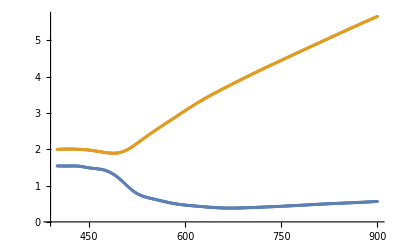

```mathematica
(Table[Flatten[{i,ReIm[nNP[i,radius[[1]] ]] }],{i,lda}]/.{x_,y_,z_}->{{x,y},{x,z}}) //Transpose //ListPlot
```

#### Mie and Extinction

```mathematica
radius = {5.78, 7.3}
radius = {3.41,4.4925}
fs = 9;
texStyle={FontFamily->"Latin Modern Math",FontSize->fs,Black};
colors=(("DefaultPlotStyle"/.(Method/. Charting`ResolvePlotTheme["Scientific",ListLinePlot]))/. Directive[x_,__]:>x);
graphsOptsTeo= {Mesh-> None,BaseStyle-> texStyle,Frame-> True, FrameStyle-> Black,ImageSize-> 300, PlotStyle-> (Directive[Dashed,#]&/@colors)};
(*SetOptions[ListLinePlot,graphsOpts];*)
wlen = Range[450,700,5.];
ticks[min_,max_]:=Join[Table[{i,NumberForm[i,{2,1}],{.01,0}},{i,0,max+1,(max)/3.}],Table[{i,,{.005,0}},{i,0,max+2,(max)/15.}]]
```

{5.78,7.3}

{3.41,4.4925}

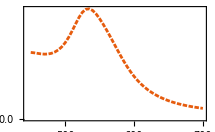
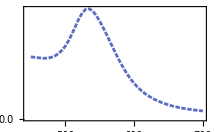

```mathematica
graphsOptsTeo= {Mesh-> None,BaseStyle-> texStyle,Frame-> True, FrameStyle-> Black,ImageSize-> 215, PlotStyle-> (Directive[colors[[#]],Dashing[{0.03,.01}/2]]&/@Range[10])};

nNP=JohnsonChristyAuRefSize[#1,#2]&;

teoGlass = Array[MieExtinctionQ[{1.5,nNP[wlen[[#2]],radius[[#1]]]},wlen[[#2]],radius[[#1]]]&,Length/@{radius,wlen}];
plotGlass = ListLinePlot[teoGlass[[#]],PlotStyle-> Directive[colors[[#]],Dashing[{0.03,.01}/2]],
FrameTicks->{{ticks,Automatic},{Automatic,Automatic}},
Axes->False,Evaluate[graphsOptsTeo],
DataRange->wlen[[{1,-1}]]
]&/@Range[1,Length[teoGlass]]
```

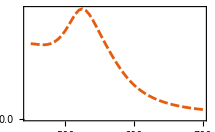
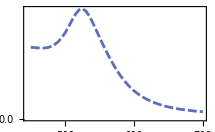

```mathematica
graphsOptsTeo= {Mesh-> None,BaseStyle-> texStyle,Frame-> True, FrameStyle-> Black,ImageSize-> 215, PlotStyle-> (Directive[colors[[#]],Dashing[{0.03,.01}/2]]&/@Range[10])};
nNP=JohnsonChristyAuRefSize[#1,#2]&;
teoH2O = Array[MieExtinctionQ[{1.33,nNP[wlen[[#2]],radius[[#1]]]},wlen[[#2]],radius[[#1]]]&,Length/@{radius,wlen}];

plotAir = ListLinePlot[teoH2O[[#]],PlotStyle-> Directive[colors[[#]],Dashing[{0.03,.01}]],
FrameTicks->{{ticks,Automatic},{Automatic,Automatic}},
Axes->False,Evaluate[graphsOptsTeo],
DataRange->wlen[[{1,-1}]]
]&/@Range[1,Length[teoH2O]]
```

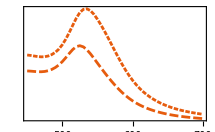
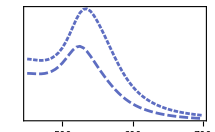

```mathematica
fl = Map[Style[#,texStyle]&,{{"Experimental Extinction Efficiency [arb. units]","Mie Theory Extinction Efficiency"},{"Wavelength [nm]",None }},{2}];
fl[[2,2]] = None;

teoPlots = MapThread[Show[{#1,#2},PlotRange->All,Filling->{1->{2}}]&,{plotAir,plotGlass}]
```

```mathematica
Export["wlength-list.txt",DeleteDuplicates[ Sort[ Join[ Range[450,700,10.], Range[520,540,0.25]] ] ] ]
```

wlength-list.txt

## Incrustamiento a = 3.41 nm

#### Normal incidence

```mathematica
files = Partition[FileNames["*.csv","1-*",3],9];
data = Map[Drop[Import[#,"Data"],5]&, files,{2}];
```

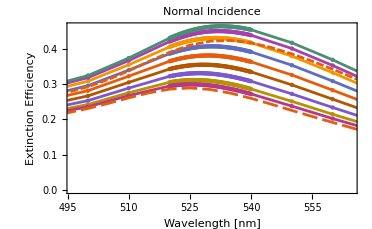

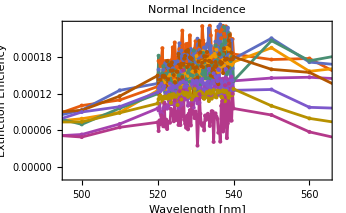

```mathematica
Show[{ListLinePlot[data[[1,;;,;;,{1,3}]],Mesh->All, ImageSize->350,
          PlotLabel->Style["Normal Incidence",FontSize->14,texStyle],
          FrameLabel-> {Style["Wavelength [nm]",texStyle], Style["Extinction Efficiency",texStyle]},
          Evaluate[graphsOptsExp]],
       teoPlots[[1]]}]
       
Show[{ListLinePlot[data[[1,;;,;;,{1,4}]],Mesh->All, ImageSize->350,
          PlotLabel->Style["Normal Incidence",FontSize->14,texStyle],
          FrameLabel-> {Style["Wavelength [nm]",texStyle], Style["Extinction Efficiency",texStyle]},
          Evaluate[graphsOptsExp]],
       teoPlots[[2]]}]
```

#### Normal incidence

```mathematica
files = Partition[FileNames["*.csv","2-*",3],9]
data = Map[Drop[Import[#,"Data"],5]&, files,{2}];
```

{{2-64/1-sPol/Supported-Internal-m000-Eff.csv,2-64/1-sPol/Supported-Internal-m025-Eff.csv,2-64/1-sPol/Supported-Internal-m050-Eff.csv,2-64/1-sPol/Supported-Internal-m075-Eff.csv,2-64/1-sPol/Supported-Internal-m100-Eff.csv,2-64/1-sPol/Supported-Internal-p025-Eff.csv,2-64/1-sPol/Supported-Internal-p050-Eff.csv,2-64/1-sPol/Supported-Internal-p075-Eff.csv,2-64/1-sPol/Supported-Internal-p100-Eff.csv},{2-64/2-pPol/Supported-Internal-m000-Eff.csv,2-64/2-pPol/Supported-Internal-m025-Eff.csv,2-64/2-pPol/Supported-Internal-m050-Eff.csv,2-64/2-pPol/Supported-Internal-m075-Eff.csv,2-64/2-pPol/Supported-Internal-m100-Eff.csv,2-64/2-pPol/Supported-Internal-p025-Eff.csv,2-64/2-pPol/Supported-Internal-p050-Eff.csv,2-64/2-pPol/Supported-Internal-p075-Eff.csv,2-64/2-pPol/Supported-Internal-p100-Eff.csv}}

```mathematica
data//Dimensions
data[[2,1,1]]
```

{2,9,104}

{450,450,0.242304,0.000099867}

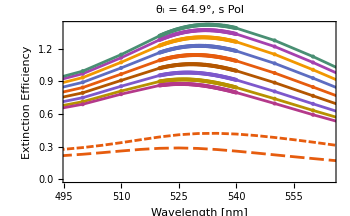

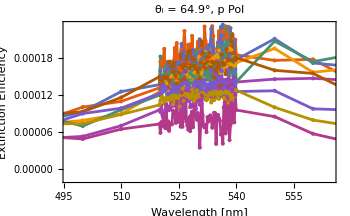

```mathematica
Show[{ListLinePlot[data[[1,;;,;;,{2,4}]],Mesh->All, ImageSize->350,
          PlotLabel->Style["θ_i = 64.9°, s Pol",FontSize->14,texStyle],
          FrameLabel-> {Style["Wavelength [nm]",texStyle], Style["Extinction Efficiency",texStyle]},
          Evaluate[graphsOptsExp]],
      teoPlots[[1]]}]
                    
Show[{ListLinePlot[data[[2,;;,;;,{2,4}]],Mesh->All, ImageSize->350,
          PlotLabel->Style["θ_i = 64.9°, p Pol",FontSize->14,texStyle],
          FrameLabel-> {Style["Wavelength [nm]",texStyle], Style["Extinction Efficiency",texStyle]},
          Evaluate[graphsOptsExp]],
     teoPlots[[1]]}]
```